# Nonlinear Dynamical Systems

Derrick Choi

Differential equations relate functions to their derivatives. They show up in fields ranging from engineering and physics to economics and biology. When the function or its derivatives appear raised to powers greater than one, or are multiplied together, the equation is nonlinear. Nonlinear differential equations often describe chaotic systems, where tiny differences in initial conditions lead to very different outcomes over time. This notebook walks through several examples of systems governed by nonlinear differential equations. Some of the computations are expensive, so evaluation may take a while.

## Numerical Methods for Differential Equations

Most nonlinear differential equations can only be solved analytically for special initial conditions, so we usually have to solve them numerically. The simplest approach is Euler’s method. Starting from a known point, you compute the slope of the tangent line there, step forward by some small increment h, and use the slope to estimate the function’s value at the new point. Then you repeat, using each new point as the starting point for the next step. More steps over a given interval means a smaller h and a better approximation. The interactive plot below shows how the approximation improves as the number of steps increases. Euler’s method is fast but not particularly accurate. The higher-order methods used by NDSolve are more precise, but the underlying idea of stepping forward using local derivative information is the same.

```mathematica
f = Compile[{{x, _Real}, {y, _Real}}, x^2 y - 1.5 y];

Euler = Compile[{{a, _Real}, {b, _Real}, {α, _Real}, {n, _Real}},
   Block[{h, T, Y, j},
    h = (b - a)/n;
    T = Table[a + (j - 1) h, {j, 1, n + 1}];
    Y = Table[α, {j, 1, n + 1}];
    For[j = 1, j <= n, j++,
     Y[[j + 1]] = Y[[j]] + h f[T[[j]], Y[[j]]]];
    Transpose[{T, Y}]]];

s1 = DSolve[{Y'[x] == x^2 Y[x] - 1.5 Y[x], Y[0] == 1}, Y, x];

plot1 = Plot[Evaluate[Y[x] /. s1], {x, 0, 2},
   PlotLegends -> {"Exact"},
   PlotLabel -> "y'(x) = x^2y(x) - 3/2y(x), y(0) = 1",
   AxesLabel -> {x, y}, ImageSize -> 400,
   PlotRange -> {{0, 2}, {0, 1}}];

slides1 = ParallelTable[
   Show[plot1,
    ListPlot[Euler[0, 2, 1, n], Joined -> True,
     PlotStyle -> Orange, PlotMarkers -> "●",
     PlotLegends -> {"Numerical"}]],
   {n, 5, 300, 1}];

Manipulate[slides1[[Steps - 4]], {Steps, 5, 300, 1}, SaveDefinitions -> True]
```

## Double Pendulum

A double pendulum is a pendulum with a second pendulum hanging from its end. The motion is governed by a pair of coupled nonlinear differential equations, and the system is chaotic.

To derive the equations of motion, we use the Lagrangian formalism. We first define the positions of the centers of mass of the two pendulum rods in terms of the generalized coordinates θ₁ and θ₂ (the angles each rod makes from the vertical, with θ = 0 pointing straight down). From these positions we compute the velocities by differentiating with respect to time, then build the kinetic energy T as the sum of translational and rotational kinetic energy for each rod:

T = .bd m v₁.b2 + .bd I θ̇₁.b2 + .bd m v₂.b2 + .bd I θ̇₂.b2

where I = (1/12) m l.b2 is the moment of inertia of a uniform rod about its center of mass. The potential energy V is solely due to acceleration due to gravity:

V = m g y₁ + m g y₂

The Lagrangian is L = T − V. Applying the Euler–Lagrange equations for each generalized coordinate,

d/dt (∂L/∂θ̇ᵢ) − ∂L/∂θᵢ = 0, i = 1, 2

gives two coupled second-order ODEs in θ₁ and θ₂. These are passed to NDSolve to be solved numerically. The example below uses equal masses (m = 1), equal lengths (l = 1), starting angles of 3π/4, and zero initial angular velocities for both pendulums.

```mathematica
g = 9.81;
l = 1;
m = 1;

x1cm = 1/2 Sin[Subscript[θ, 1][t]];
y1cm = -1/2 Cos[Subscript[θ, 1][t]];

x2cm = l Sin[Subscript[θ, 1][t]] + 1/2 Sin[Subscript[θ, 2][t]];
y2cm = -l Cos[Subscript[θ, 1][t]] - 1/2 Cos[Subscript[θ, 2][t]];

v1sq = D[x1cm, t]^2 + D[y1cm, t]^2;
v2sq = D[x2cm, t]^2 + D[y2cm, t]^2;

Ibar = 1/12 m l^2;

Tbar1 = 1/2 m v1sq + 1/2 Ibar (Subscript[θ, 1]'[t])^2;
Tbar2 = 1/2 m v2sq + 1/2 Ibar (Subscript[θ, 2]'[t])^2;
T = Tbar1 + Tbar2;

V = m g y1cm + m g y2cm;

L = T - V;

ELeq1 = D[D[L, Subscript[θ, 1]'[t]], t] - D[L, Subscript[θ, 1][t]] == 0;
ELeq2 = D[D[L, Subscript[θ, 2]'[t]], t] - D[L, Subscript[θ, 2][t]] == 0;

s2 = NDSolve[
   {ELeq1, ELeq2,
    Subscript[θ, 1][0] == (3 π)/4, Subscript[θ, 2][0] == (3 π)/4,
    Subscript[θ, 1]'[0] == 0, Subscript[θ, 2]'[0] == 0},
   {Subscript[θ, 1], Subscript[θ, 2]}, {t, 0, 20}];

xa[t_] := l Cos[Subscript[θ, 1][t] - π/2] /. s2
ya[t_] := l Sin[Subscript[θ, 1][t] - π/2] /. s2

xb[t_] := (l Cos[Subscript[θ, 1][t] - π/2] +
            l Cos[Subscript[θ, 2][t] - π/2]) /. s2
yb[t_] := (l Sin[Subscript[θ, 1][t] - π/2] +
            l Sin[Subscript[θ, 2][t] - π/2]) /. s2

slides2 = ParallelTable[
   Rasterize[Show[
    ParametricPlot[
     Evaluate[Flatten[{xb[t], yb[t]}]],
     {t, If[f - 1.5 < 0, 0, f - 1.5], f},
     ColorFunction -> Function[{x, y, t}, Directive[Opacity[t]]],
     ColorFunctionScaling -> True, ImageSize -> 450,
     PlotRange -> {-2.5, 2.5}, Axes -> False],
    Graphics[{Thick, Darker[Gray],
      Line[{{0, 0}, Flatten[{xa[f], ya[f]}]}],
      Line[{Flatten[{xa[f], ya[f]}], Flatten[{xb[f], yb[f]}]}]}]], "Image"],
   {f, 0.032, 20, 0.032}];

ListAnimate[slides2, 25, AnimationRunning -> False]
```

The motion of the double pendulum is highly sensitive to initial conditions. The two simulations below use identical parameters and starting conditions for the inner pendulum. The outer pendulums start with the same angular velocity and a difference in angle of only Δθ = 0.0001. At first the two systems move in sync, but they quickly diverge until their motions look completely unrelated.

```mathematica
sa = NDSolve[
   {ELeq1, ELeq2,
    Subscript[θ, 1][0] == (3 π)/4, Subscript[θ, 2][0] == (3 π)/4,
    Subscript[θ, 1]'[0] == 0, Subscript[θ, 2]'[0] == 0},
   {Subscript[θ, 1], Subscript[θ, 2]}, {t, 0, 20}];

sb = NDSolve[
   {ELeq1, ELeq2,
    Subscript[θ, 1][0] == (3 π)/4,
    Subscript[θ, 2][0] == (3 π)/4 + 0.0001,
    Subscript[θ, 1]'[0] == 0, Subscript[θ, 2]'[0] == 0},
   {Subscript[θ, 1], Subscript[θ, 2]}, {t, 0, 20}];

x1a[t_] := l Cos[Subscript[θ, 1][t] - π/2] /. sa
y1a[t_] := l Sin[Subscript[θ, 1][t] - π/2] /. sa
x2a[t_] := (l Cos[Subscript[θ, 1][t] - π/2] +
             l Cos[Subscript[θ, 2][t] - π/2]) /. sa
y2a[t_] := (l Sin[Subscript[θ, 1][t] - π/2] +
             l Sin[Subscript[θ, 2][t] - π/2]) /. sa

x1b[t_] := l Cos[Subscript[θ, 1][t] - π/2] /. sb
y1b[t_] := l Sin[Subscript[θ, 1][t] - π/2] /. sb
x2b[t_] := (l Cos[Subscript[θ, 1][t] - π/2] +
             l Cos[Subscript[θ, 2][t] - π/2]) /. sb
y2b[t_] := (l Sin[Subscript[θ, 1][t] - π/2] +
             l Sin[Subscript[θ, 2][t] - π/2]) /. sb

slides3 = ParallelTable[
   Rasterize[Graphics[
    {Thick, RGBColor[204/255, 121/255, 167/255],
     Line[{{0, 0}, Flatten[{x1a[f], y1a[f]}]}],
     Line[{Flatten[{x1a[f], y1a[f]}], Flatten[{x2a[f], y2a[f]}]}],
     Thick, RGBColor[0, 158/255, 115/255],
     Line[{{0, 0}, Flatten[{x1b[f], y1b[f]}]}],
     Line[{Flatten[{x1b[f], y1b[f]}], Flatten[{x2b[f], y2b[f]}]}]},
    PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 450], "Image"],
   {f, 0.032, 20, 0.032}];

ListAnimate[slides3, 25, AnimationRunning -> False]
```

## Swinging Atwood’s Machine

A swinging Atwood’s machine consists of two masses connected by an inextensible string that passes over two pulleys. One mass (the “swinging” mass, m = 1) can swing freely in a plane, while the other (the “counterweight” mass, m = μ) is constrained to move vertically.

The system has two degrees of freedom: r, the distance of the swinging mass from its pulley, and θ, the angle the string makes with the downward vertical. The kinetic energy has contributions from both masses:

T = .bd m (ṙ.b2 + r.b2θ̇.b2) + .bd μ ṙ.b2

The swinging mass moves in polar coordinates, so its speed squared is ṙ.b2 + r.b2θ̇.b2. The counterweight moves along the string, so its speed is just |ṙ|. For the potential energy, take the swinging mass’s pulley as the reference height. The swinging mass hangs at depth r cos θ below the pulley, and the counterweight hangs at height r above its minimum height:

V = −m g r cos θ + μ g r 

Forming L = T − V and applying the Euler–Lagrange equations for r and θ gives two coupled second-order ODEs. We solve them numerically with NDSolve. The example below uses a mass ratio μ = 4.5 and initial conditions θ = −π/2, θ̇ = 0, r = 500, and ṙ = 0.

```mathematica
g = 9.81;

xsw = r[t] Sin[θ[t]];
ysw = -r[t] Cos[θ[t]];

Tsw = 1/2 (D[xsw, t]^2 + D[ysw, t]^2);
Tcw = 1/2 μ r'[t]^2;
Tatwood = Tsw + Tcw;

Vatwood = g ysw + μ g r[t];

Latwood = Tatwood - Vatwood;

ELatwoodθ = D[D[Latwood, θ'[t]], t] -
                   D[Latwood, θ[t]] == 0;
ELatwoodr = D[D[Latwood, r'[t]], t] -
            D[Latwood, r[t]] == 0;

μval = 4.5;

s3 = NDSolve[
   {ELatwoodθ /. μ -> μval,
    ELatwoodr /. μ -> μval,
    r[0] == 500, θ[0] == -π/2,
    r'[0] == 0, θ'[0] == 0},
   {r, θ}, {t, 0, 4500}];

xAtwood[t_] := (r[t] Cos[θ[t] - π/2]) /. s3
yAtwood[t_] := (r[t] Sin[θ[t] - π/2]) /. s3

slides4 = ParallelTable[
   Rasterize[Show[
    ParametricPlot[Flatten[{xAtwood[t], yAtwood[t]}],
     {t, 0, f}, PlotStyle -> {Black, Thickness[0.002]},
     ImageSize -> 400,
     PlotRange -> {{-700, 700}, {-700, 500}},
     PlotPoints -> 31, Axes -> False,
     PlotLabel -> "μ = 4.5"],
    Graphics[{Thick, Darker[Gray],
      Line[{{0, 0}, Flatten[{xAtwood[f], yAtwood[f]}]}],
      Line[{{0, 0}, {210, 0}}],
      Line[{{210, 0},
        {210, -(700 - Norm[Flatten[{xAtwood[f], yAtwood[f]}]])}}],
      Darker[Red],
      Disk[Flatten[{xAtwood[f], yAtwood[f]}], 25],
      Darker[Blue],
      Disk[{210, -(700 - Norm[Flatten[{xAtwood[f], yAtwood[f]}]])}, 35]}]], "Image"],
   {f, 0.536, 300, 0.536}];

ListAnimate[slides4, 25, AnimationRunning -> False]
```

For certain mass ratios the swinging mass traces out complex but periodic orbits. The ratio μ = 4.5 used above is one such case. The figure below shows the trajectory for μ = 3 integrated over a long time interval.

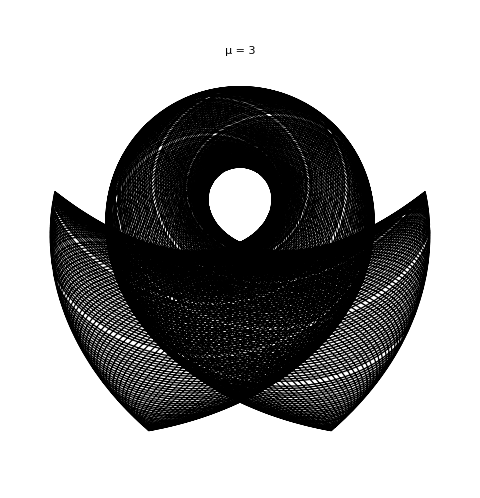

```mathematica
μval = 3;

s4 = NDSolve[
   {ELatwoodθ /. μ -> μval,
    ELatwoodr /. μ -> μval,
    r[0] == 500, θ[0] == -π/2,
    r'[0] == 0, θ'[0] == 0},
   {r, θ}, {t, 0, 5220}];

xA3[t_] := (r[t] Cos[θ[t] - π/2]) /. s4
yA3[t_] := (r[t] Sin[θ[t] - π/2]) /. s4

Framed[
 ParametricPlot[Flatten[{xA3[t], yA3[t]}],
  {t, 0, 5220}, PlotRange -> {{-530, 530}, {-750, 350}},
  PlotStyle -> {Black, Thickness[0.002]}, Axes -> False,
  ImageSize -> 480, PlotPoints -> 300,
  PlotLabel -> "μ = 3"],
 FrameStyle -> Thin]
```

Here are trajectories for mass ratios of 5, 6, 16, and 19. Each produces a distinct pattern, illustrating the dependence of the orbit on μ.

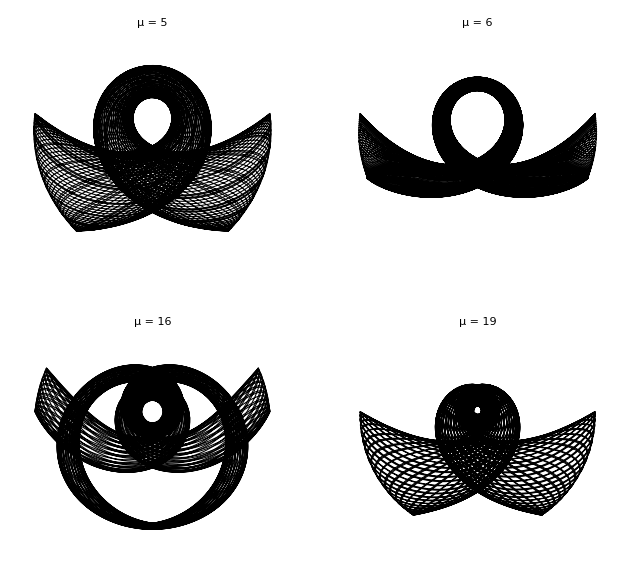

```mathematica
data = ParallelTable[
   Block[{sol, xf, yf},
    sol = NDSolve[
       {ELatwoodθ /. μ -> μval,
        ELatwoodr /. μ -> μval,
        r[0] == 500, θ[0] == -π/2,
        r'[0] == 0, θ'[0] == 0},
       {r, θ}, {t, 0, 2300}];
    xf[t_] := (r[t] Cos[θ[t] - π/2]) /. sol;
    yf[t_] := (r[t] Sin[θ[t] - π/2]) /. sol;
    ParametricPlot[Flatten[{xf[t], yf[t]}],
     {t, 0, 2300},
     PlotRange -> {{-530, 530}, {-600, 320}},
     PlotStyle -> {Black, Thickness[0.0025]}, Axes -> False,
     ImageSize -> 300, PlotPoints -> 300,
     PlotLabel -> "μ = " <> ToString[μval]]
   ],
   {μval, {5, 6, 16, 19}}];

GraphicsGrid[Partition[data, 2], Frame -> All, ImageSize -> 630]
```

## Three-Body Problem

The three-body problem is the problem of taking the initial positions and velocities of three point masses and calculating their trajectories using Newton’s laws of motion and gravitation. There is no general closed-form analytic solution, and the system is generically chaotic.

Each mass has three degrees of freedom, giving nine degrees of freedom for the system in total. Let r₁, r₂, and r₃ be position vectors for the three masses. The kinetic energy is the sum of the individual kinetic energies:

T = .bd m₁ |ṙ₁|.b2 + .bd m₂ |ṙ₂|.b2 + .bd m₃ |ṙ₃|.b2

The total potential energy is the sum of the gravitational potential energies between each pair of the three masses:

V = −G m₁ m₂ / |r₁ − r₂| − G m₁ m₃ / |r₁ − r₃| − G m₂ m₃ / |r₂ − r₃|

With L = T − V, the Euler–Lagrange equation for each coordinate qᵢ ∈ {x₁, y₁, z₁, x₂, y₂, z₂, x₃, y₃, z₃},

d/dt (∂L/∂q̇ᵢ) − ∂L/∂qᵢ = 0

produces nine coupled second-order ODEs. These are solved numerically with NDSolve. The gravitational constant is set to G = 1 for simplicity, and the masses are m₁ = 1.3, m₂ = 0.9, m₃ = 0.091.

```mathematica
G = 1;
m1 = 1.3;
m2 = 0.9;
m3 = 0.091;

r1 = {x1[t], y1[t], z1[t]};
r2 = {x2[t], y2[t], z2[t]};
r3 = {x3[t], y3[t], z3[t]};

r12sq = (x1[t] - x2[t])^2 + (y1[t] - y2[t])^2 + (z1[t] - z2[t])^2;
r13sq = (x1[t] - x3[t])^2 + (y1[t] - y3[t])^2 + (z1[t] - z3[t])^2;
r23sq = (x2[t] - x3[t])^2 + (y2[t] - y3[t])^2 + (z2[t] - z3[t])^2;

T3body = 1/2 m1 D[r1, t].D[r1, t] +
         1/2 m2 D[r2, t].D[r2, t] +
         1/2 m3 D[r3, t].D[r3, t];

V3body = -(G m1 m2)/(√r12sq) - (G m1 m3)/(√r13sq) - (G m2 m3)/(√r23sq);

L3body = T3body - V3body;

coords = {x1, y1, z1, x2, y2, z2, x3, y3, z3};
eqs3body = Table[
   D[D[L3body, q'[t]], t] - D[L3body, q[t]] == 0,
   {q, coords}];

ics = {
   x1[0] == 0, y1[0] == 0, z1[0] == 0,
   x1'[0] == 0, y1'[0] == 0, z1'[0] == 0.6,
   x2[0] == 1, y2[0] == 0, z2[0] == 0,
   x2'[0] == 0, y2'[0] == 1, z2'[0] == 0,
   x3[0] == -1, y3[0] == 0, z3[0] == 0,
   x3'[0] == 0, y3'[0] == -0.6, z3'[0] == -0.1};

s6 = NDSolve[
   Join[eqs3body, ics],
   {x1, y1, z1, x2, y2, z2, x3, y3, z3},
   {t, 0, 14}];

pts1 = Table[{x1[t], y1[t], z1[t]} /. s6 // Flatten,{t, 0,14, 1/60}];
pts2 = Table[{x2[t], y2[t], z2[t]} /. s6 // Flatten,{t, 0,14, 1/60}];
pts3 = Table[{x3[t], y3[t], z3[t]} /. s6 // Flatten,{t, 0,14, 1/60}];

mtot = m1 + m2 + m3;
cenFirst = (m1 pts1[[1]] + m2 pts2[[1]] + m3 pts3[[1]]) / mtot;
cenLast = (m1 pts1[[-1]] + m2 pts2[[-1]] + m3 pts3[[-1]]) / mtot;

camOffset = {3, -3, 2};
tMax = 14.0;
vel = (cenLast - cenFirst) / tMax;

nFrames = Length[pts1];
dt = tMax / (nFrames - 1.0);

slides5 = ParallelTable[Block[{tNow, target, camPos}, tNow = (i - 1) dt;
target = cenFirst + vel tNow;
camPos = target + camOffset;
Rasterize[Graphics3D[{{RGBColor[204 / 255, 121 / 255, 167 / 255], Line[pts1[[;;i]]],Sphere[pts1[[i]], 0.08]}, {RGBColor[230 / 255, 159 / 255, 0], Line[pts2[[;;i]]],Sphere[pts2[[i]], 0.08]}, {RGBColor[0, 158 / 255, 115 / 255], Line[pts3[[;;i]]],Sphere[pts3[[i]], 0.05]}}, PlotRange -> {{-2, 3}, {-3, 7}, {-1, 5}}, ViewVector -> {camPos, target}, ViewAngle -> Pi / 3, Ticks -> None, Boxed -> False,Axes -> True, AxesEdge -> {{1, -1}, {-1, -1}, {-1, 1}}, FaceGrids -> {{-1, 0, 0}, {0, 1, 0}, {0, 0, -1}}], "Image"]], {i, 1, nFrames, 1}];

ListAnimate[slides5, 60, AnimationRunning -> False]
```